```mathematica
data=Import["/u/he/valba/Github/negatitivy/ran_negativity/mathematica/re40","TSV"];
```

```mathematica
list={};
For[i=1,i≤Length[ToExpression[data⟦1,1⟧]],i++,Print[i];temp=Table[ToExpression[data⟦k,1⟧]⟦i⟧,{k,1,Length[data]}];AppendTo[list,{i,Mean[temp],StandardDeviation[temp]/(√Length[temp])}];]
```

1

2

3

4

5

6

7

```mathematica
Export["/u/he/valba/Github/negatitivy/ran_negativity/mathematica/ExactL256.dat",list];
```

1

2

3

4

5

6

7

8

```mathematica
list[[2,1]]
```

Part::partw: Part 2 of {{{0.531066, 1.32669, 1.39365, 1.14848, 1.75284, 1.10161, 1.85847, 1.75697}, « 49 », « 99950 »}} does not exist.

{{{0.531066,1.32669,1.39365,1.14848,1.75284,1.10161,1.85847,1.75697},99999}}⟦2,1⟧
 |  |  |  |

```mathematica
list[[]]
```

```mathematica
list
```

{{1,{0.910944,1.09957,1.22513,1.28167,1.35737+3.79849×10^-20 ⅈ,1.3702+2.86358×10^-18 ⅈ,1.43678+5.0035×10^-17 ⅈ,1.41339+2.35131×10^-16 ⅈ}}}

```mathematica
data[[2,2]]
```

Part::partw: Part 2 of {"{0.7268196626159225, 1.3734619102953431, 1.9621617838742371, 1.8064640391708717, 1.9149482464042318, 1.430330432161622, 1.6767549212209956, 2.2786650201493144}"} does not exist.

{{{0.531066335350165, 1.3266933926549185, 1.3936461553881776, 1.1484847230257007, 1.7528438796766272, 1.1016117991432774, 1.8584675015843037, 1.7569746181891819}},99998,{{1.3003239286476629, 0.5478837720438785…1.6943442986383548, 1.9125425880172573}}}⟦2,2⟧
 |  |  |  |

```mathematica
ToExpression[data[[3,1]]]
```

{0.800664,1.36309,1.4441,1.9117,1.45802,0.99909,1.58913,0.992739+8.50168×10^-16 ⅈ}

```mathematica
list
```

{}

```mathematica
Length[ToExpression[data[[1,1]]]]
```

8

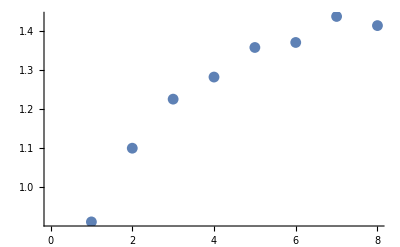

```mathematica
list//ListPlot
```

```mathematica
Log[2.]/3
```

0.231049

```mathematica
Log[2.]/3
```

0.231049

```mathematica
75*5+650
```

1025

```mathematica
list
```

{{1,0.910944,0.0011787},{2,1.09957,0.00122436},{3,1.22513,0.00123129},{4,1.28167,0.00134758},{5,1.35737+3.79849×10^-20 ⅈ,0.00125042},{6,1.3702+2.86358×10^-18 ⅈ,0.0014705},{7,1.43678+5.0035×10^-17 ⅈ,0.00121497},{8,1.41339+2.35131×10^-16 ⅈ,0.00158738}}

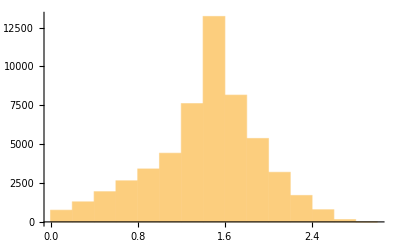

```mathematica
Histogram[Table[ToExpression[data[[i,1]]][[8]],{i,1,Length[data]}]]
```

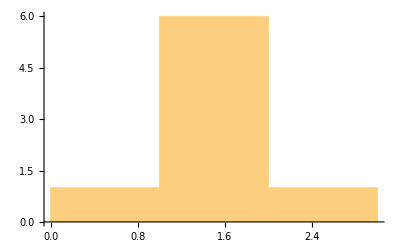

```mathematica
Histogram[ToExpression[data[[2,1]]]]
```

```mathematica
list
```

{{1,0.910686,0.00465616},{2,1.1036,0.00482897},{3,1.23332,0.00476211},{4,1.28427,0.00531844},{5,1.36416,0.00497347},{6,1.37354+2.01155×10^-18 ⅈ,0.00588412},{7,1.44032+5.04783×10^-17 ⅈ,0.00481656},{8,1.41544+2.30786×10^-16 ⅈ,0.00645723}}

```mathematica
Log[2.]/3
```

0.231049

```mathematica
(1.03)^1000
```

6.87424×10^12

```mathematica
1604/8.
```

200.5

```mathematica
Log[2.]/3
```

0.231049

```mathematica
list
```

{{1,0.904435,0.0011816},{2,1.10859,0.00121455},{3,1.21649,0.00126167},{4,1.2937,0.00130492},{5,1.35302+2.04915×10^-20 ⅈ,0.00133552},{6,1.39556+1.09618×10^-18 ⅈ,0.00139527},{7,1.4412+1.65808×10^-17 ⅈ,0.00138496},{8,1.46692+1.01713×10^-16 ⅈ,0.00147086},{9,1.50207+2.58703×10^-16 ⅈ,0.00142323},{10,1.5191+4.60381×10^-16 ⅈ,0.00154395},{11,1.55094+6.996×10^-16 ⅈ,0.00143476},{12,1.5602+9.60744×10^-16 ⅈ,0.00161695},{13,1.58374+1.24469×10^-15 ⅈ,0.00143917},{14,1.58876+1.56172×10^-15 ⅈ,0.00168016},{15,1.61302+1.89915×10^-15 ⅈ,0.0014222},{16,1.60611+2.25451×10^-15 ⅈ,0.00173907}}

```mathematica
7700/8.
```

962.5

```mathematica
90./110
```

0.818182

```mathematica
29/33.
```

0.878788